```mathematica
SetDirectory[NotebookDirectory[]];
```

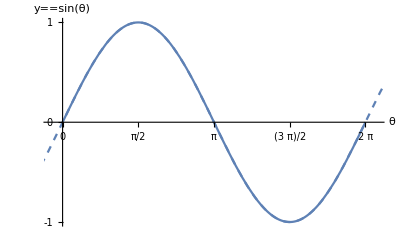

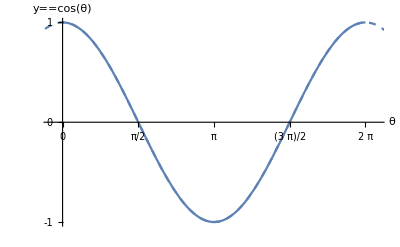

```mathematica
Show[
Plot[Sin[x],{x,0,2Pi}],
Plot[Sin[x],{x,-Pi,3Pi},PlotStyle->Dashed],
Ticks->{Range[0,4]*Pi/2,Range[-1,1]},
PlotRange->{{0-0.25,2Pi+0.25},{-1,1}},
AxesLabel->{HoldForm[θ],HoldForm[y==Sin[θ]]},
AxesStyle->Directive[16]
]
Export[{"sine.pdf","sine.svg"},%];
Show[
Plot[Cos[x],{x,0,2Pi}],
Plot[Cos[x],{x,-Pi,3Pi},PlotStyle->Dashed],
Ticks->{Range[0,4]*Pi/2,Range[-1,1]},
PlotRange->{{0-0.25,2Pi+0.25},{-1,1}},
AxesLabel->{HoldForm[θ],HoldForm[y==Cos[θ]]},
AxesStyle->Directive[16]
]
Export[{"cosine.pdf","cosine.svg"},%];
```

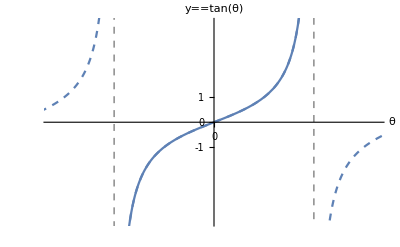

```mathematica
Show[
Plot[Tan[x],{x,-Pi/2,Pi/2}],
Plot[Tan[x],{x,-Pi,3Pi},PlotStyle->Dashed],
ContourPlot[x==Pi/2,{x,-5,5},{y,-5,5},ContourStyle->{Thin,Dashed,Gray}],
ContourPlot[x==-Pi/2,{x,-5,5},{y,-5,5},ContourStyle->{Thin,Dashed,Gray}],
Ticks->{Range[-4,4]*Pi/2,Range[-1,1]},
PlotRange->{{-Pi/2-1,Pi/2+1},{-4,4}},
AxesLabel->{HoldForm[θ],HoldForm[y==Tan[θ]]},
AxesStyle->Directive[16]
]
Export[{"tangent.pdf","tangent.svg"},%];
```